# Finding the concentrations of a bibi reaction using rate law/kinetics.

1. Here I use the definition of Keq = kf/kb

```mathematica
kf[Tf_] := 8.3*10^8*Exp[-6900/(1.987*Tf)];
kb[Ta_] := 1.92*10^7*Exp[-10000/(1.987 * Ta)]; Keq = kf[500]/kb[500]
```

979.26

2a)
For the reaction A + B ⇌ C + D, (dA(t))/dt= - k_f A(t) B(t) + k_b C(t) D(t), where
A(t) = A(0) - η(t)
B(t) = B(0) -η(t)
C(t) = C(0) + η(t)
D(t) = D(0) + η(t)
-(dη(t))/dt = - k_f (A(0)-η(t)) (B(0) - η(t))+ k_b (C(0)+η(t) (D(0)+η(t))
Here I flip the equation, so that NO2 and NOCL are A and B, and the forward rate constant is now kb and the backward rate constant is now kf. This is for clarity as I can now see the extent of reaction as starting with only reactants.

```mathematica
Clear[η, t,kf, kb, A0, B0, C0, D0]
e0[3]=Coefficient[ kf (A0-η[t]) (B0-η[t]) - kb (C0+η[t]) (D0+η[t]),η[t],0]//FullSimplify;
e1[3]=Coefficient[ kf (A0-η[t]) (B0-η[t]) - kb (C0+η[t]) (D0+η[t]),η[t],1]//FullSimplify;
e2[3] =Coefficient[ kf (A0-η[t]) (B0-η[t]) - kb (C0+η[t]) (D0+η[t]),η[t],2];
Δ[3]= e1[3]^2-4 e0[3] e2[3]//FullSimplify
Clear[η]
η[t_]=η[t]/.(DSolve [{η'[t]==e0 + e1 η[t]+ e2 η[t]^2 },η[t],t]//Flatten);
η[t_]=η[t]/.e1^2->  4 e0 e2+Δ;
η[t_] = η[t] /.(Solve[η[0] == 0, C[1]]//Flatten);
η[t_] = η[t] // TrigToExp // FullSimplify;
η[t_] = η[t] /. (e1 ^2 -> (4e0 e2 + Δ))// Cancel;
eta[3][t_]=η[t]/.{e0->e0[3],e1->e1[3],e2->e2[3]}//FullSimplify
```

-4 (kb-kf) (C0 D0 kb-A0 B0 kf)+((C0+D0) kb+(A0+B0) kf)^2

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(-2 C0 D0 kb+2 A0 B0 kf)/((C0+D0) kb+(A0+B0) kf+√Δ Coth[(t √Δ)/2])

```mathematica
Clear[η,t]
kf[Tf_] := 8.3*10^8*Exp[-6900/(1.987*Tf)];
kb[Ta_] := 1.92*10^7*Exp[-10000/(1.987 * Ta)]; 
η[t_] := (-2 C0 D0 kb+2 A0 B0 kf)/((C0+D0) kb+(A0+B0) kf+√Δ Coth[(t √Δ)/2])
Clear [ruleΔ]
ruleΔ = Δ -> -4 (kb-kf) (C0 D0 kb-A0 B0 kf)+((C0+D0) kb+(A0+B0) kf)^2;
Δ /. ruleΔ;
η[t_]=η[t]/.ruleΔ //FullSimplify;
initialC = {A0 -> 1, B0 -> 1.5, C0 -> 0, D0 -> 0};
rateConst={kf->kb[500],kb->kf[500]} ;
η[t]/.initialC/.rateConst ;
NO2[t_] := A0 - η[t]/.initialC/.rateConst;
Limit [NO2[t], t -> Infinity]
NOCL[t_] := B0 - η[t]/.initialC/.rateConst;
Limit [NOCL[t], t -> Infinity]
NO2CL[t_] := C0 + η[t]/.initialC/.rateConst;
Limit [NO2CL[t], t -> Infinity]
NO[t_] := D0 + η[t]/.initialC/.rateConst;
Limit [NO[t], t -> Infinity]
```

0.962099

1.4621

0.0379009

0.0379009

2b)

```mathematica
Clear[x]
kf[Tf_] := 8.3*10^8*Exp[-6900/(1.987*Tf)]
kb[Ta_] := 1.92*10^7*Exp[-10000/(1.987 * Ta)]
kf[500]/kb[500];
Solve[(1+x)(1.5+x)/x^2 == kf[500]/kb[500], x];
concNO2 = 1-0.03790088001749749
concNOCL = 1.5 -0.03790088001749749
concNO =0.03790088001749749
concNO2CL = 0.03790088001749749
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.962099

1.4621

0.0379009

0.0379009

3)

```mathematica
Clear[t]
Solve[NO2[t]== 0.9740233, t];
t=2.64017*10^-5
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.0000264017

4) These graphs make sense as NO2 should be used up to create NO.

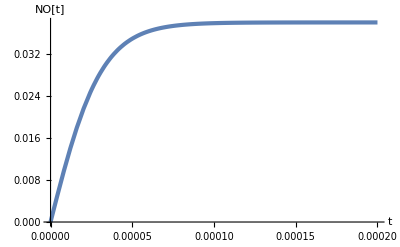

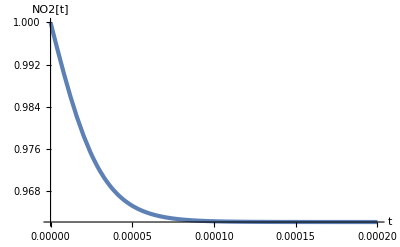

```mathematica
Clear[t]
plNO=Plot[NO[t],{t,0, 2*10^-4},
PlotRange->All, 
PlotStyle->AbsoluteThickness[3],
AxesLabel->{"t","NO[t]"}] 
plNO2=Plot[NO2[t],{t,0, 2*10^-4},
PlotRange->All, 
PlotStyle->AbsoluteThickness[3],
AxesLabel->{"t","NO2[t]"}]
```

5) Again these graphs make sense with Keq in mind. Creation of NO and the ‘distruction’ of NO2.

0.956533

0.0434668

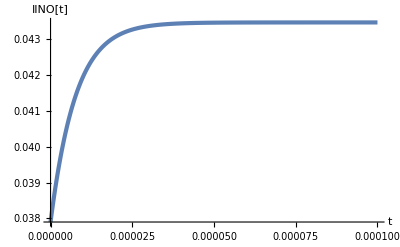

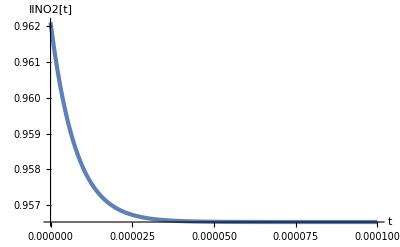

```mathematica
eqConc = {A0 -> 0.962099, B0 -> 1.4620991199825024, C0 -> 0.03790088001749748, D0 -> 0.03790088001749748};
raisedConst={kf->kb[550],kb->kf[550]} ;
IINO2[t_] := 0.962099 - η[t]/.eqConc/.raisedConst;
IINO[t_] :=0.03790088001749748 + η[t]/.eqConc/.raisedConst;
Limit [IINO2[t], t -> Infinity]
Limit [IINO[t], t -> Infinity]
plIINO=Plot[IINO[t],{t,0, 1*10^-4},
PlotRange->All, 
PlotStyle->AbsoluteThickness[3],
AxesLabel->{"t","IINO[t]"}] 
plIINO2=Plot[IINO2[t],{t,0, 1*10^-4},
PlotRange->All, 
PlotStyle->AbsoluteThickness[3],
AxesLabel->{"t","IINO2[t]"}]
```